# Inlämningsuppgift 1: Problemlösning

IX1307 Problemlösning i Matematik, Inlämningsuppgift 1a, HT2022

Notebook mall

## 1. Inledning

Denna uppgift går ut på att lösa ett antal matematiska problem med hjälp av Mathematica och skriva en kort rapport direkt i en egen Notebook. Rapporten skall, för varje uppgift, beskriva: problemet, figur, ange namn på variabler, lösningen till problemet inklusive resonemang och sedan diskutera resultatet. Ni ska sedan granska varandras uppgifter jämföra lösningar.

Plagiering är inte tillåten, och källor måste anges när ni refererar till annat material. Lämna in både en pdf-fil och notebook-filen i Canvas. Pdf-filen behövs för plagiatkontroll, då *.nb inte är accepeterad i URKUND.

## 2. Nyttiga funktioner i Mathematica

Här är en kort beskrivning av några funktioner som kan vara nyttiga att känna till för att lösa problemen nedan. För mer information om funktionerna se Wolfram Documentation under hjälp-menyn.

#### Ekvationer och Olikheter

Ta reda på hur kommandona Solve, Reduce, och Eliminate fungerar med hjälp av Wolfram Documentation. Studera sedan följande sida
"tutorial/ManipulatingEquationsAndInequalities"paclet:tutorial/ManipulatingEquationsAndInequalities#5158
för hur man löser olikheter och ekvationer med absolutbelopp.

Exempelvis för att lösa ekvationen |x-4|=4 kan man använda funktionen Reduce.

```mathematica
Reduce[Abs[x-4]==4, x, Reals]
```

x==0||x==8

Reals talar om vilken typ av tal som avses för x. Domänen kan vara Heltal (Integers), Reella tal (Reals) eller Komplexa tal (Complex).

#### Komplexa tal

Den imaginära enheten representeras av ett versalt I i Mathematica.

```mathematica
I*I
```

Roten av ett negativt tal :

```mathematica
Sqrt[-4]
```

Algebra med komplexa tal fungera som vanligt:

```mathematica
(4+3 I)/(2-I)
```

```mathematica
z1=Exp[2+9 I]
```

Funktionen N kan användas för att beräkna numeriska närmevärde av exempelvis z_1

```mathematica
N[z1]
```

eller av andra tal. Här är Pi med 50 siffrors noggranhet:

```mathematica
N[Pi, 50]
```

Olika funktioner kan sedan användas för att manipulera komplexa tal:

```mathematica
z2=4+3I;
```

Realdel:

```mathematica
Re[z2]
```

Imaginärdel

```mathematica
Im[z2]
```

Komplexa konjugatet till z_2

```mathematica
Conjugate[z2]
```

och till z_1

```mathematica
Conjugate[z1]
```

Absolutbeloppet till z_2

```mathematica
Abs[z2]
```

Argumentet till z_1

```mathematica
Arg[z2]
```

För att grafiskt representera komplexa talplanet används ListPlot. Vi börjar med att skapa en lista av talen:

```mathematica
cn={z1, Conjugate[z1], z2, Conjugate[z2]}
```

Sedan kan listan av tal konverteras till en list av talpar {realdel, imaginärdel}

```mathematica
pp=Table[{Re[cn[[i]]], Im[cn[[i]]]}, {i, 1, 4}]
```

Här är en de komplexa talen ritade i det komplexa talplanet:

```mathematica
ListPlot[pp, AxesLabel->{"Re", "Im"}, AspectRatio->Automatic,PlotMarkers->{Automatic, Medium},Epilog->{ EdgeForm[Red],FaceForm[],Rectangle[{pp[[3,1]], pp[[3,2]]}, {pp[[2, 1]], pp[[2, 2]]}], }]
```

#### Summor

Sum används för att en serie, dvs en summa av en talföljd. Om det finns ett utryck för varje element i serien kan den skrivas enligt:

```mathematica
Sum[n^2, {n, 1, 10}]
```

I detta fall serien för talföljden n^2 där n∈[1, 10].
Om man vill summera de 100 första primtalen så kan man använda funktionen Prime. För att bestämma det 10:e primtalet kan man använda

```mathematica
Prime[10]
```

Funktionen Sum kan då användas för att beräkna serien av de 100 första primtalen.

```mathematica
Sum[Prime[i], {i, 1, 100}]
```

#### Trigonometri

Denna sida innehåller information om hur trigonometriska funktioner fungerar i Mathematica: "Trigonometric Functions"paclet:guide/TrigonometricFunctions

#### Logik

Denna sida innehåller information om hur Logik fungerar i Mathematica: "Logic & Boolean Algebra"paclet:guide/LogicAndBooleanAlgebra. Titta speciellt på “Tutorials” längst ner på sidan.

#### Mängdlära

På följande sida finns en instruktion om hur Mathematica kan hantera enkla mängdoperationer: "Lists as Sets"paclet:tutorial/ListsAsSets.

## 3. Problem

Lös nedanstående problem. Problemets lösning och resultat skall innehålla visualisering där det är relevant.

### Polynomekvation

Hitta lösningarna till polynomekvationen: 2 x^4-74/3 x^3+253/6 x^2+111/2 x-105=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.

### Olikhet

Lös uppgift 21, 22, 25 och 26  i kapitel 3 i boken Matematisk kommunikation, argumentation och skapande. Ge ett exakt svar. I de fall det är lämpligt illustrera lösningsområdet grafiskt.

### Binomisk ekvation

Finn lösningen till ekvationen z^5=-3+3i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

### Arean av en cirkel och närmevärde till Pi

En kvadrat kan skrivas in i en cirkel och en cirkel kan skrivas in i en kvadrat, vilket ger figuren nedan. Antag att cirkeln har radien r=1.

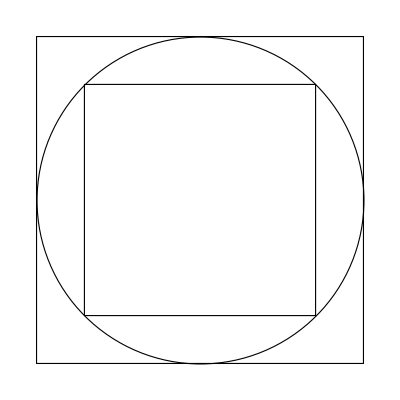

```mathematica
Show[Graphics[{FaceForm[None],EdgeForm[{Black}],Polygon[{{-1/Sqrt[2],-1/Sqrt[2]},{-1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],1/Sqrt[2]} ,{1/Sqrt[2], -1/Sqrt[2]}}],Disk[{0, 0}],Polygon[{{-1, -1}, {-1, 1},{1, 1},{1, -1}}]}]]
```

Från figuren kan vi konstatera att cirkelns area är mindre än 2^2=4 och större än (2/√2)^2=2. Det betyder att vi kan bestämma π=3±1. Dvs medelvärdet av 4+2 och det absoluta felet till närmevärdet. Då cirkelns area i detta fall är π r^2= π, så är detta också en metod att bestämma ett närmevärde till π. 
Vi kan också se arean för en kvadrat som fyrsidig polygon där arean kan bestämmas av fyra trianglar.
Använd ovanstående metod med reglebundna polygoner med fler sidor än fyra och beräkna ett mer exakt värde på π. Jämför sedan med värdet på Pi i Mathematica (se nedan med 10 siffor). Du får använda trigonometriska funktioner för att bestämma arean av trianglarna. 
Rita en graf för hur min och max värdet konvergerar mot Pi som en funktion av antal sidor på polygonen.

```mathematica
N[Pi, 10]
```

3.141592654